```mathematica
t  = {{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
Solve[Det[t]==E^(I κ),d]
```

{{d→(b c+ⅇ^(ⅈ κ))/a}}

```mathematica
t = t/.%[[1]]
```

{{a,b},{c,(b c+ⅇ^(ⅈ κ))/a}}

```mathematica
Simplify[(((t.ConjugateTranspose[t]//MatrixForm)==(IdentityMatrix[2]//MatrixForm))),{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ3,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals]}]
```

(1 | 0
0 | 1)==(a Conjugate[a]+b Conjugate[b] | a Conjugate[c]+(b (ⅇ^(-ⅈ Conjugate[κ])+Conjugate[b c]))/Conjugate[a]
c Conjugate[a]+((b c+ⅇ^(ⅈ κ)) Conjugate[b])/a | c Conjugate[c]+((b c+ⅇ^(ⅈ κ)) (ⅇ^(-ⅈ Conjugate[κ])+Conjugate[b c]))/(a Conjugate[a]))

```mathematica
t = t/.{a->E^(I ϕ1)Cos[θ1],b->E^(I ϕ2)Sin[θ1]}
```

{{ⅇ^(ⅈ ϕ1) Cos[θ1],ⅇ^(ⅈ ϕ2) Sin[θ1]},{c,ⅇ^(-ⅈ ϕ1) Sec[θ1] (ⅇ^(ⅈ κ)+c ⅇ^(ⅈ ϕ2) Sin[θ1])}}

```mathematica
Simplify[(((t.ConjugateTranspose[t]//MatrixForm)==(IdentityMatrix[2]//MatrixForm))),{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ3,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals],Element[κ,Reals]}]
```

(1 | 0
0 | 1)==(1 | ⅇ^(ⅈ ϕ1) (Conjugate[c] Sec[θ1]+ⅇ^(-ⅈ (κ-ϕ2)) Tan[θ1])
ⅇ^(-ⅈ (ϕ1+ϕ2)) (c ⅇ^(ⅈ ϕ2) Sec[θ1]+ⅇ^(ⅈ κ) Tan[θ1]) | Sec[θ1] (Sec[θ1]+c ⅇ^(-ⅈ (κ-ϕ2)) Tan[θ1])+Conjugate[c] Sec[θ1] (c Sec[θ1]+ⅇ^(ⅈ (κ-ϕ2)) Tan[θ1]))

```mathematica
Solve[ⅇ^(ⅈ ϕ1) (Conjugate[c] Sec[θ1]+ⅇ^(-ⅈ (κ-ϕ2)) Tan[θ1])==0,c]
```

{{c→-ⅇ^(ⅈ Conjugate[κ]-ⅈ Conjugate[ϕ2]) Conjugate[Sin[θ1]]}}

```mathematica
t = t/.%[[1]]
```

{{ⅇ^(ⅈ ϕ1) Cos[θ1],ⅇ^(ⅈ ϕ2) Sin[θ1]},{-ⅇ^(ⅈ Conjugate[κ]-ⅈ Conjugate[ϕ2]) Conjugate[Sin[θ1]],ⅇ^(-ⅈ ϕ1) Sec[θ1] (ⅇ^(ⅈ κ)-ⅇ^(ⅈ ϕ2+ⅈ Conjugate[κ]-ⅈ Conjugate[ϕ2]) Conjugate[Sin[θ1]] Sin[θ1])}}

```mathematica
t = Simplify[t,{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals],Element[κ,Reals]}];
```

```mathematica
t//MatrixForm
```

(ⅇ^(ⅈ ϕ1) Cos[θ1] | ⅇ^(ⅈ ϕ2) Sin[θ1]
-ⅇ^(ⅈ (κ-ϕ2)) Sin[θ1] | ⅇ^(ⅈ (κ-ϕ1)) Cos[θ1])

```mathematica
Det[t]//Simplify
```

ⅇ^(ⅈ κ)

```mathematica
tt = Simplify[(t/ⅇ^(ⅈ ϕ1)/.κ->2ϕ1),{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ3,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals],Element[κ,Reals]}]/.{ϕ1->ϕ+ϕ2}
```

{{Cos[θ1],ⅇ^(-ⅈ ϕ) Sin[θ1]},{-ⅇ^(ⅈ ϕ) Sin[θ1],Cos[θ1]}}

```mathematica
tt = Simplify[(E^(I α)t),{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ3,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals],Element[κ,Reals]}]//MatrixForm
```

(ⅇ^(ⅈ (α+ϕ1)) Cos[θ1] | ⅇ^(ⅈ (α+ϕ2)) Sin[θ1]
-ⅇ^(ⅈ (α+κ-ϕ2)) Sin[θ1] | ⅇ^(ⅈ (α+κ-ϕ1)) Cos[θ1])

```mathematica
tt
```

```mathematica
Clear[eg]
```

```mathematica
eg[θ1_,ϕ1_,ϕ2_] = Simplify[(E^(-I (ϕ1))t/.κ->0),{Element[ϕ1,Reals],Element[ϕ2,Reals],Element[ϕ3,Reals],Element[ϕ4,Reals],Element[θ1,Reals],Element[θ2,Reals],Element[κ,Reals]}]
```

{{Cos[θ1],ⅇ^(-ⅈ (ϕ1-ϕ2)) Sin[θ1]},{-ⅇ^(-ⅈ (ϕ1+ϕ2)) Sin[θ1],ⅇ^(-2 ⅈ ϕ1) Cos[θ1]}}

```mathematica
polarForm[m_]:=Map[Abs[#] e^(I Arg[#])&,m,{2}]
```

```mathematica
polarForm[IdentityMatrix[2]]
```

{{1,0},{0,1}}

```mathematica
Clear[polarForm]
```

```mathematica
f//@IdentityMatrix[3]
```

f[{f[{f[1],f[0],f[0]}],f[{f[0],f[1],f[0]}],f[{f[0],f[0],f[1]}]}]

```mathematica
I//polarForm
```

e^((ⅈ π)/2)

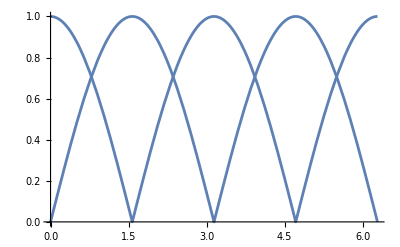

```mathematica
Plot[Abs[{Re[E^(I x)],Im[E^(I x)]}],{x,0,2Pi}]
```

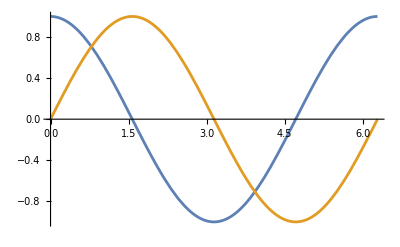

```mathematica
Plot[{Cos[a],Sin[a]},{a,0,2Pi}]
```

```mathematica
eg[a,b,c]
```

{{Cos[a],ⅇ^(-ⅈ (b-c)) Sin[a]},{-ⅇ^(-ⅈ (b+c)) Sin[a],ⅇ^(-2 ⅈ b) Cos[a]}}

```mathematica
({Re[#],Im[#]}&/@Flatten[eg[a,b,c]])//Flatten
```

{Re[Cos[a]],Im[Cos[a]],Re[ⅇ^(-ⅈ (b-c)) Sin[a]],Im[ⅇ^(-ⅈ (b-c)) Sin[a]],-Re[ⅇ^(-ⅈ (b+c)) Sin[a]],-Im[ⅇ^(-ⅈ (b+c)) Sin[a]],Re[ⅇ^(-2 ⅈ b) Cos[a]],Im[ⅇ^(-2 ⅈ b) Cos[a]]}

```mathematica
Manipulate[Plot[({Re[#],Im[#]}&/@Flatten[eg[Pi/2,b,c]])//Flatten,{b,0,Pi}],{c,0,Pi}]
```

```mathematica
Manipulate[Plot[({Re[#],Im[#]}&/@Flatten[eg[a,b,c]])//Flatten,{a,0,2Pi}],{b,0,2Pi},{c,0,2Pi}]
```

```mathematica
eg
```

```mathematica
Det[t.t//FullSimplify]//FullSimplify
```

ⅇ^(2 ⅈ κ)

```mathematica
Det[t]//FullSimplify
```

ⅇ^(ⅈ κ)

```mathematica
E^(-I ϕ2+Pi)
```

```mathematica
ⅇ^(π-ⅈ ϕ2)
```

```mathematica
E^(I(2))//N
```

-0.416147+0.909297 ⅈ

```mathematica
E^(I(2+Pi))==-E^(I(2))//N
```

True